```mathematica
zSetDirectory[NotebookDirectory[]];
```

```mathematica
Get["article/allPrimes.mx"];
```

```mathematica
Table[ListLinePlot[Log@Differences[allPrimes[[x,;;20]]],PlotLabel->x],{x,2,11}]//TableForm
```

```mathematica
JaccardDissimilarity[Table[diffs1[[x]]<diffs1[[x+1]],{x,Length[diffs1]-1}],Table[diffs3[[x]]<diffs3[[x+1]],{x,Length[diffs3]-1}]]//N
```

```mathematica
Table[diffs1[[x]]<diffs1[[x+1]],{x,Length[diffs1]-1}]Table[diffs3[[x]]<diffs3[[x+1]],{x,Length[diffs3]-1}]
```

False

```mathematica
diffs6=Differences[allPrimes[[6,;;10000]]];
diffs4=Differences[allPrimes[[4,;;10000]]];
diffs1=Differences[allPrimes[[2,;;10000]]];
diffs3=Differences[allPrimes[[3,;;10000]]];
```

```mathematica
Position[Table[(diffs3[[x]]<diffs3[[x+1]])==(diffs1[[x]]<diffs1[[x+1]]),{x,Length[diffs]-1}],False]
```

{{2},{15},{36},{39},{46},{54},{55},{73},{102},{107},{110},{118},{129},{160},{164},{184},{187},{194},{199},{218},{239},{271},{272},{291},{339},{358},{387},{419},{426},{464},{465},{508},{520},{553},{599},{605},{621},{629},{633},{667},{682},{683},{702},{709},{710},{733},{761},{791},{813},{821},{822},{829},{830},{882},{896},{952},{962},{988},{990},{1020},{1085},{1090},{1161},{1173},{1217},{1256},{1293},{1299},{1318},{1365},{1376},{1386},{1407},{1414},{1425},{1429},{1491},{1498},{1502},{1510},{1511},{1530},{1544},{1553},{1567},{1594},{1595},{1702},{1726},{1727},{1770},{1773},{1788},{1806},{1838},{1842},{1843},{1853},{1854},{1873},{1884},{1903},{1910},{1917},{1921},{1938},{1953},{1958},{1966},{1991},{2004},{2009},{2010},{2046},{2086},{2087},{2101},{2110},{2137},{2206},{2209},{2210},{2220},{2223},{2233},{2254},{2272},{2275},{2280},{2284},{2297},{2315},{2333},{2378},{2431},{2456},{2463},{2470},{2473},{2491},{2510},{2600},{2601},{2643},{2646},{2657},{2677},{2680},{2709},{2731},{2799},{2807},{2821},{2827},{2864},{2876},{2877},{2898},{2926},{2932},{2959},{2967},{3030},{3061},{3111},{3148},{3170},{3180},{3186},{3212},{3235},{3249},{3253},{3254},{3276},{3287},{3303},{3304},{3338},{3344},{3376},{3442},{3484},{3486},{3536},{3549},{3625},{3651},{3660},{3690},{3698},{3702},{3722},{3745},{3761},{3798},{3808},{3814},{3830},{3844},{3853},{3887},{3904},{4010},{4029},{4094},{4117},{4190},{4208},{4210},{4212},{4229},{4241},{4244},{4285},{4288},{4292},{4320},{4337},{4340},{4349},{4384},{4409},{4412},{4431},{4448},{4460},{4509},{4583},{4626},{4630},{4649},{4712},{4716},{4739},{4773},{4844},{4877},{4896},{4899},{4933},{4947},{4966},{4992},{5004},{5043},{5097},{5150},{5173},{5175},{5257},{5265},{5275},{5362},{5382},{5402},{5463},{5464},{5495},{5512},{5539},{5558},{5563},{5571},{5577},{5607},{5659},{5668},{5683},{5689},{5690},{5696},{5720},{5755},{5776},{5791},{5861},{5880},{5885},{5899},{5924},{5927},{5937},{5960},{5976},{6003},{6063},{6070},{6087},{6100},{6108},{6191},{6200},{6210},{6252},{6253},{6283},{6287},{6324},{6363},{6366},{6369},{6386},{6387},{6407},{6414},{6463},{6532},{6546},{6563},{6586},{6623},{6657},{6664},{6691},{6725},{6737},{6751},{6780},{6808},{6827},{6832},{6860},{6905},{7033},{7064},{7065},{7109},{7126},{7129},{7169},{7193},{7229},{7255},{7258},{7331},{7345},{7346},{7354},{7386},{7407},{7411},{7438},{7439},{7445},{7451},{7466},{7523},{7531},{7532},{7540},{7560},{7569},{7574},{7620},{7621},{7657},{7676},{7684},{7710},{7728},{7729},{7760},{7782},{7817},{7823},{7832},{7858},{7865},{7918},{7919},{7925},{7936},{7967},{7989},{7995},{8011},{8058},{8063},{8090},{8091},{8106},{8145},{8146},{8193},{8201},{8229},{8230},{8281},{8289},{8351},{8373},{8386},{8448},{8486},{8494},{8498},{8608},{8619},{8631},{8632},{8654},{8655},{8669},{8711},{8761},{8778},{8823},{8828},{8829},{8836},{8887},{8906},{8919},{8941},{8986},{8989},{9018},{9105},{9106},{9184},{9185},{9222},{9243},{9244},{9252},{9282},{9285},{9314},{9370},{9415},{9456},{9466},{9576},{9667},{9697},{9700},{9717},{9867},{9895},{9905},{9933},{9935},{9938},{9943},{9948},{9952},{9979},{9997},{9998}}

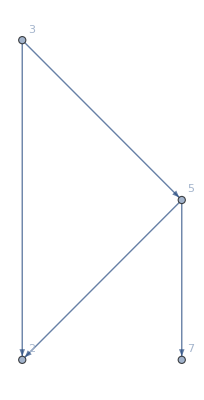
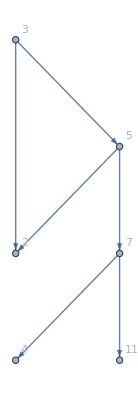
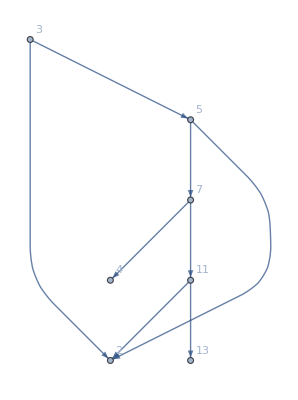
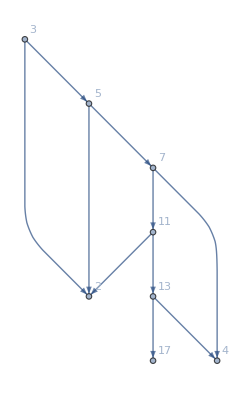
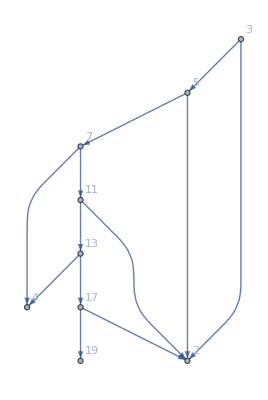
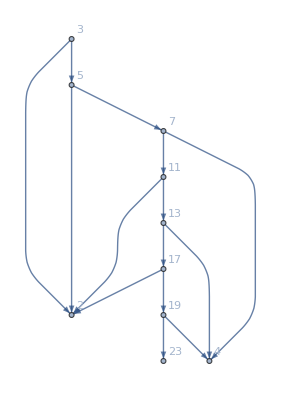
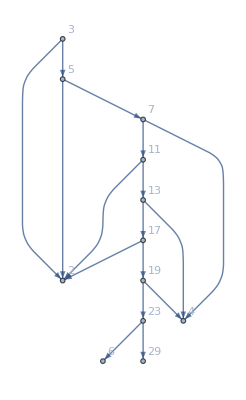
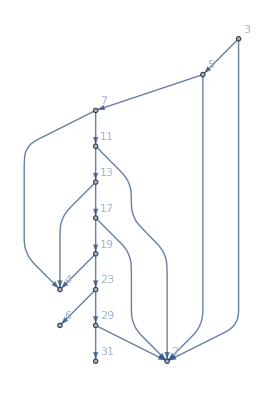

```mathematica
t=Table[Nest[Differences,allPrimes[[2,2;;100]],n],{n,0,8}];
cons=Table[Flatten@Table[{t[[1,x]]->t[[1,x+1]]-t[[1,x]],t[[1,x]]->t[[1,x+1]]},{x,y}],{y,2,30}];
Table[Graph[Union[s,s],VertexLabels->"Name"],{s,cons}]
```

```mathematica
Position[t[[2]],2]
```

{{1},{2},{4},{6},{9},{12},{16},{19},{25},{27}}

```mathematica
Position[t[[2]],4]
```

{{3},{5},{7},{11},{13},{18},{21},{24},{26},{28}}

```mathematica
Position[t[[2]],6]
```

{{8},{10},{14},{15},{17},{20},{22}}

```mathematica
Position[t[[2]],8]
```

{{23}}

```mathematica
Table[Position[t[[2]],x],{x,2,20,2}]//TableForm
```

1 | 2 | 4 | 6 | 9 | 12 | 16 | 19 | 25 | 27 | 32 | 34 | 40 | 42 | 44 | 48 | 51 | 56 | 59 | 63 | 68 | 80 | 82 | 88 | 97 | 
3 | 5 | 7 | 11 | 13 | 18 | 21 | 24 | 26 | 28 | 30 | 37 | 43 | 47 | 49 | 58 | 62 | 64 | 69 | 74 | 77 | 84 | 87 | 89 | 92 | 94
8 | 10 | 14 | 15 | 17 | 20 | 22 | 31 | 35 | 36 | 38 | 39 | 50 | 53 | 54 | 55 | 57 | 66 | 70 | 72 | 73 | 75 | 83 | 85 | 95 | 
23 | 71 | 76 | 78 | 86 | 91 | 93 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
33 | 41 | 52 | 60 | 67 | 79 | 81 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
45 | 46 | 90 | 96 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29 | 61 | 65 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
98 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Table[t[[2,x]]->t[[3,x]],{x,Length@t[[1]]-2}]//Graph
```

-Graphics-

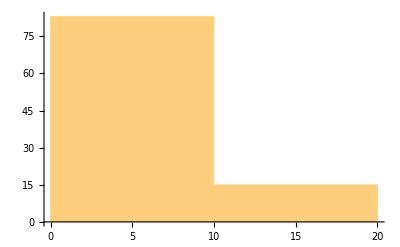

```mathematica
Histogram[t[[2]],3]
```